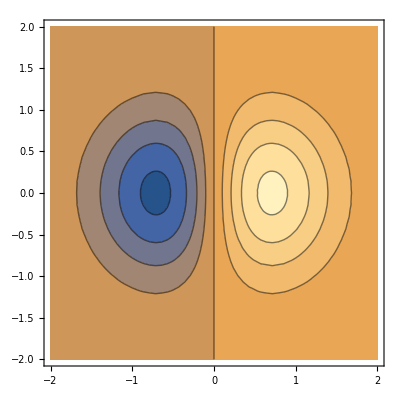

```mathematica
ContourPlot[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ContourLabels->Automatic]
```

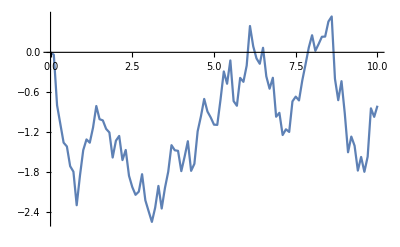

```mathematica
Block[{f,x,t},f=RandomFunction[WienerProcess[],{0,10,0.1}];Print[ListLinePlot[f]];]
```

```mathematica
Simplify[Element[234/100,Rationals]]
```

True

```mathematica
(* Approximate differential equations *)
```

```mathematica
Block[
{f,x,t,xmax,tmax,func,Δx=10^(-3),Δt=10^(-6)},
xmax=45;tmax=1;
func=NDSolveValue[{D[f[x,t],t]==(1-f[x,t])(1-f[x,t]+f[x,t]^2)D[f[x,t],x]Δx/Δt-1/Δt f[x,t](f[x,t]^2-2f[x,t]+2)(f[x,t]^3-f[x,t]^2+2f[x,t]-1),f[x,0]==Sin[π x/xmax]^2,f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
ContourPlot[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},
Contours->70,PlotLegends->True, ContourLabels->Automatic,ColorFunction->Hue
]
]
```

-Graphics-

```mathematica
Block[
{f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=10^(-3);tmax=10^(-3);
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==If[0≤x<xmax/2,2x/xmax,2(1-x/xmax)],f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
Plot3D[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->Hue]
]
```

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 33829.1 at t = 0.001 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=10^(-2);tmax=100Δt;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Sin[π x/xmax]^2,f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
Plot3D[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->Hue,AxesLabel->{x,t,f1},PlotRange->{{0,xmax},{0,tmax},{0,1}},PlotLegends->Automatic]
]
```

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 339.486 at t = 1.×10^-7 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-

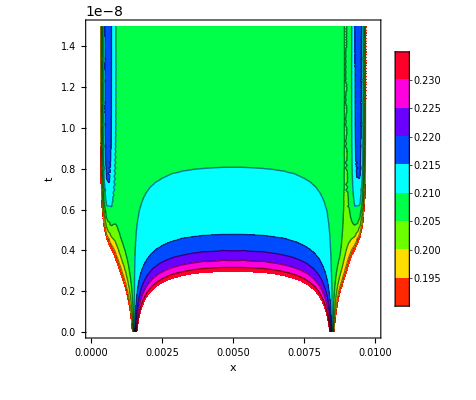

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=10^(-2);tmax=15Δt;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Sin[π x/xmax]^2,f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
ContourPlot[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->Hue,AxesLabel->{x,t,f1},PlotLegends->Automatic]
]
```

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=1;tmax=5Δt;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Sin[π x/xmax]^2,f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
Plot3D[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->Hue,AxesLabel->{x,t,f1},PlotRange->{{0,xmax},{0,tmax},{0,1}},PlotLegends->Automatic]
]
```

-Graphics3D-

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 339.486 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

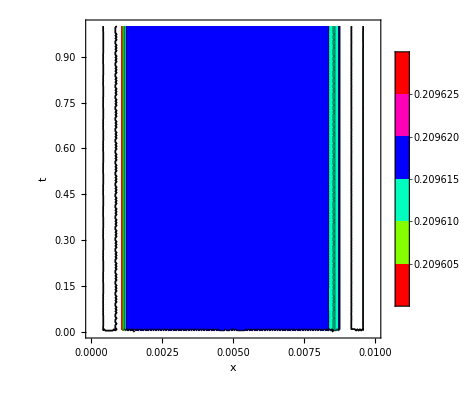

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=10^(-2);tmax=1;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Sin[π x/xmax]^2,f[0,t]==0,f[xmax,t]==0},f[x,t],{x,0,xmax},{t,0,tmax}];
ContourPlot[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->Hue,AxesLabel->{x,t,f1},PlotLegends->Automatic]
]
```

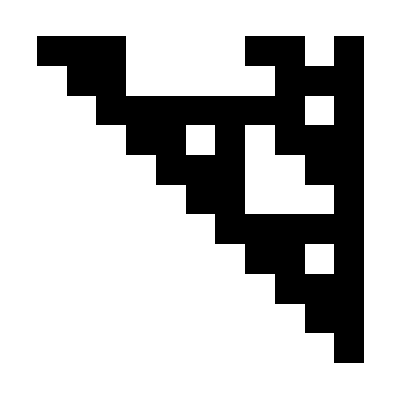

```mathematica
With[{M=10},ArrayPlot[CellularAutomaton[110,Join[Table[0,{n,1,M}],{1}],M],DataReversed->True]]
```

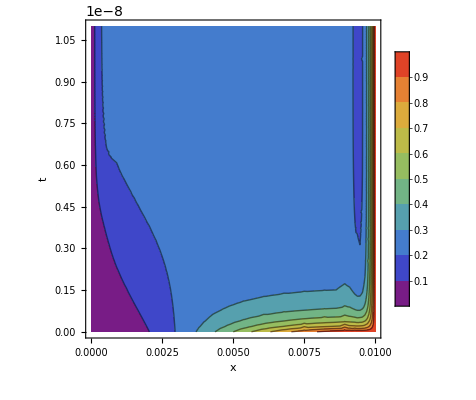

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9)},
xmax=10^(-2);tmax=11Δt;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Sin[π /2(x/xmax)]^2,f[0,t]==0,f[xmax,t]==1},f[x,t],{x,0,xmax},{t,0,tmax}];
ContourPlot[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->"Rainbow",AxesLabel->{x,t,f1},PlotLegends->Automatic,PlotRange->All]
]
```

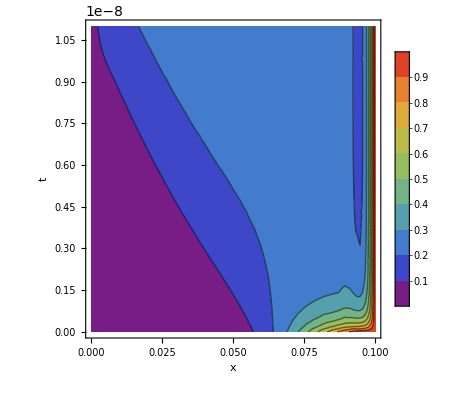

```mathematica
Block[
{f1,f,x,t,xmax,tmax,func,Δx=10^(-6),Δt=10^(-9),σ},
xmax=10^(-1);tmax=11Δt;σ=1/5xmax;
func=NDSolveValue[{f[x,t] + Δt D[f[x,t],t] == -f[x,t] (2+(-2+f[x,t]) f[x,t]) (-1+f[x,t] (2+(-1+f[x,t]) f[x,t]))-Δx (-1+f[x,t]) (1+(-1+f[x,t]) f[x,t])^2 Derivative[1,0][f][x,t]+Δx^2 f[x,t]^2 (1+(-1+f[x,t]) f[x,t]) (Derivative[1,0][f][x,t])^2+Δx^3 (-1+f[x,t]) f[x,t]^2 (Derivative[1,0][f][x,t])^3,f[x,0]==Exp[-(x-xmax)^2/2/σ^2],f[0,t]==0,f[xmax,t]==1},f[x,t],{x,0,xmax},{t,0,tmax}];
ContourPlot[(func)/.{x->x1,t->t1},{x1,0,xmax},{t1,0,tmax},ColorFunction->"Rainbow",AxesLabel->{x,t,f1},PlotLegends->Automatic,PlotRange->All]
]
```